```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

Syntax::stresc: Unknown string escape \U.

Syntax::stresc: Unknown string escape \s.

Syntax::stresc: Unknown string escape \D.

Syntax::stresc: Unknown string escape \U.

Syntax::stresc: Unknown string escape \s.

Syntax::stresc: Unknown string escape \D.

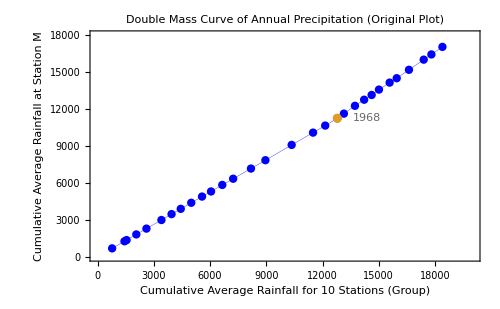

The {Slope, Y-intercept} of the plot from 1950 to 1968 = {0.879075,-13.9166}

The {Slope, Y-intercept} of the plot from 1968 to 1979 = {1.03046,-1904.81}

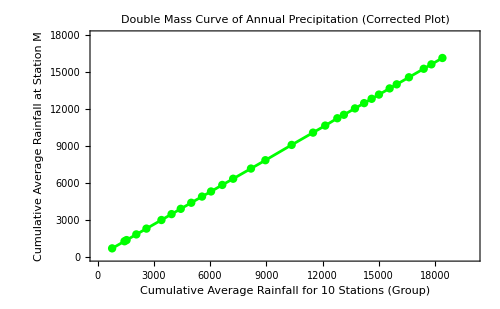

Year | Average Annual Rainfall (M) | Average Annual Rainfall (Group) | Original Cumulative Rainfall (M) | Cumulative Rainfall (Group) | Corrected Cumulative Rainfall (M)
1950 | 676 | 780 | 676 | 780 | 676
1951 | 578 | 660 | 1254 | 1440 | 1254
1952 | 95 | 110 | 1349 | 1550 | 1349
1953 | 462 | 520 | 1811 | 2070 | 1811
1954 | 472 | 540 | 2283 | 2610 | 2283
1955 | 699 | 800 | 2982 | 3410 | 2982
1956 | 479 | 540 | 3461 | 3950 | 3461
1957 | 431 | 490 | 3892 | 4440 | 3892
1958 | 493 | 560 | 4385 | 5000 | 4385
1959 | 503 | 575 | 4888 | 5575 | 4888
1960 | 415 | 480 | 5303 | 6055 | 5303
1961 | 531 | 600 | 5834 | 6655 | 5834
1962 | 504 | 580 | 6338 | 7235 | 6338
1963 | 828 | 950 | 7166 | 8185 | 7166
1964 | 679 | 770 | 7845 | 8955 | 7845
1965 | 1244 | 1400 | 9089 | 10355 | 9089
1966 | 999 | 1140 | 10088 | 11495 | 10088
1967 | 573 | 650 | 10661 | 12145 | 10661
1968 | 596 | 646 | 11257 | 12791 | 11257
1969 | 375 | 350 | 11632 | 13141 | 11538.
1970 | 635 | 590 | 12267 | 13731 | 12056.7
1971 | 497 | 490 | 12764 | 14221 | 12487.4
1972 | 386 | 400 | 13150 | 14621 | 12839.
1973 | 438 | 390 | 13588 | 15011 | 13181.9
1974 | 568 | 570 | 14156 | 15581 | 13683.
1975 | 356 | 377 | 14512 | 15958 | 14014.4
1976 | 685 | 653 | 15197 | 16611 | 14588.4
1977 | 825 | 787 | 16022 | 17398 | 15280.2
1978 | 426 | 410 | 16448 | 17808 | 15640.7
1979 | 612 | 588 | 17060 | 18396 | 16157.6

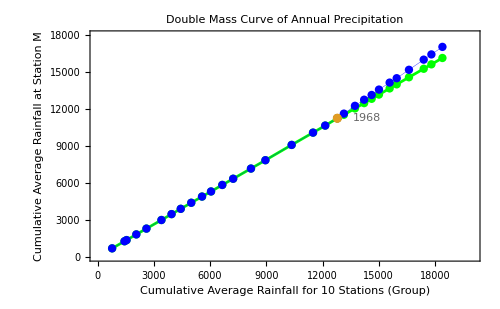

```mathematica
dataset=Import["C:\Users\swarupa\Downloads\DataDoubleMassCurveAssignment.txt","Table"];


dataset1=Table[{dataset[[i,1]],dataset[[i,2]],dataset[[i,3]],0,0},{i,2,31}];
For[j=1;dataset1[[1,4]]=dataset1[[1,2]];dataset1[[1,5]]=dataset1[[1,3]],j<30,j++,
dataset1[[j+1,4]]=dataset1[[j,4]]+dataset1[[j+1,2]];
dataset1[[j+1,5]]=dataset1[[j,5]]+dataset1[[j+1,3]]
];


discrepancy=If[MemberQ[{dataset1[[19,{5,4}]]},#],Style[#,Red]]&/@dataset1[[All,{5,4}]];


originalplot=Show[
ListLinePlot[dataset1[[All,{5,4}]],PlotStyle->{Blue,Thickness[0.0005]},Mesh->All],
ListPlot[{discrepancy,Callout[{dataset1[[19,{5,4}]]},"1968",Automatic]},LabelingFunction->Automatic],
Frame->True,LabelStyle->{FontFamily->"Arial",FontSize->12,Directive[Bold,Black]},FrameLabel->{"Cumulative  Average  Rainfall  for  10 Stations (Group)","Cumulative  Average  Rainfall  at  Station  M"},ImageSize->500,PlotRange->{{0,20000},{0,18000}},PlotLabel->"Double Mass Curve of Annual Precipitation (Original Plot)"
]


fit1=LinearModelFit[dataset1[[1;;19,{5,4}]],{x1,1},x1];
fit1[x1];
coeff1=fit1["BestFitParameters"];
Print["The {Slope, Y-intercept} of the plot from 1950 to 1968 = ",coeff1]
fit2=LinearModelFit[dataset1[[19;;30,{5,4}]],{x2,1},x2];
fit2[x2];
coeff2=fit2["BestFitParameters"];
Print["The {Slope, Y-intercept} of the plot from 1968 to 1979 = ",coeff2]


datasetN=Table[0,{k,30}];
datasetN[[1;;19]]=dataset1[[1;;19,{5,4}]];
For[m=20,m<31,m++,
datasetN[[m]]={dataset1[[m,5]],(coeff1[[1]]*dataset1[[m,5]])+coeff1[[2]]}
];


correctedplot=ListLinePlot[datasetN,Mesh->All,PlotStyle->{Green,Thickness[0.004]},Frame->True,LabelStyle->{FontFamily->"Arial",FontSize->12,Directive[Bold,Black]},FrameLabel->{"Cumulative  Average  Rainfall  for  10 Stations (Group)","Cumulative  Average  Rainfall  at  Station  M"},ImageSize->500,PlotRange->{{0,20000},{0,18000}},PlotLabel->"Double Mass Curve of Annual Precipitation (Corrected Plot)"
]


datasetP=Table[{0,0,0,0,0,0},{n,1,31}];
datasetP[[1]]={"Year","Average Annual Rainfall (M)","Average Annual Rainfall (Group)","Original Cumulative Rainfall (M)","Cumulative Rainfall (Group)","Corrected Cumulative Rainfall (M)"};
For[q=1,q<6,q++,
For[p=2,p<32,p++,
datasetP[[p,q]]=dataset1[[p-1,q]];
datasetP[[p,6]]=datasetN[[p-1,2]];
]
]
Print[TableForm[datasetP]]


Show[correctedplot,originalplot,PlotLabel->"Double Mass Curve of Annual Precipitation"]
```